# Лабораторная работа № 5. Доска Гальтона.

Выполнила студентка ММФ БГУ
 1 к, 5 гр. Шклярик В.С.
 4 ноября 2021

Функция galtonBoard вычисляет координаты точек доски Гальтона. На входе: размер доски(натуральное число n).
На выходе: список n списков, в каждом из которых координаты точек соответствующего уровня доски.

```mathematica
galtonBoard[n_]:=Table[{(2 k-i)/2,(-i √3)/2},{i,0,n-1},{k,0,i}];
```

```mathematica
galtonBoard[3]
```

{{{0,0}},{{-1/2,-(√3)/2},{1/2,-(√3)/2}},{{-1,-√3},{0,-√3},{1,-√3}}}

Второй вариант функции, вычисляющей координаты точек доски.

```mathematica
galton2[1]={{0,0}};
galton2[n_]:=Module[{vect={-1/2,(-√3)/2},lastIt=galton2[n-1]},Append[(#+vect&/@lastIt),(#+vect&/@lastIt//Last)+{1,0}]];
```

```mathematica
galton2Board[1]={{0,0}};
galton2Board[n_]:=Append[galton2Board[n-1],galton2[n]]
```

```mathematica
galton2Board[3]
```

{{0,0},{{-1/2,-(√3)/2},{1/2,-(√3)/2}},{{-1,-√3},{0,-√3},{1,-√3}}}

```mathematica
galtonBoardView[n_]:=Graphics[{AbsolutePointSize[12],Red,Point/@galtonBoard[n]}]
```

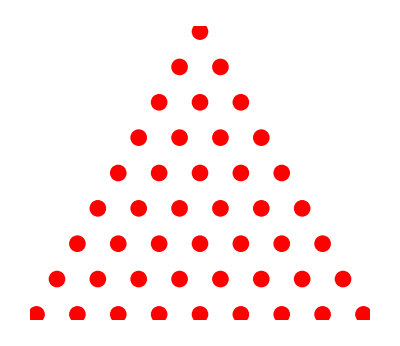

```mathematica
galtonBoardView[9]
```

Введем вспомогательную функцию q,  которая из одного списка {a1,a2,..,an} создает два списка вида {a1, a2,..,an, an}, {a1, a2,..,an, an+1}.

```mathematica
q[list_]:=Append[list,#]&/@{Last[list],Last[list]+1};
```

Функция giveAllRoutes вычисляет в виде списка списков все возможные маршруты шарика для доски заданного размера n.

```mathematica
ClearAll[giveAllRoutes];
giveAllRoutes[1]:={1};
giveAllRoutes[2]:=q[{1}];
giveAllRoutes[3]:=q/@q[{1}];
giveAllRoutes[n_]:=Nest[q/@#&,Flatten[giveAllRoutes[n-1],1],1]/;n>3;
```

```mathematica
giveAllRoutes[5]
```

{{{1,1,1,1,1},{1,1,1,1,2}},{{1,1,1,2,2},{1,1,1,2,3}},{{1,1,2,2,2},{1,1,2,2,3}},{{1,1,2,3,3},{1,1,2,3,4}},{{1,2,2,2,2},{1,2,2,2,3}},{{1,2,2,3,3},{1,2,2,3,4}},{{1,2,3,3,3},{1,2,3,3,4}},{{1,2,3,4,4},{1,2,3,4,5}}}

Функция galtonRoute для доски заданного размера n вычисляет случайный маршрут шарика и выдает его в виде списка координат точек,  соответствующих этому маршруту.

```mathematica
galtonRoute[n_]:=MapThread[Part,{galtonBoard[n],RandomChoice[Flatten[giveAllRoutes[n],1]]}]
```

```mathematica
galtonRoute[5]
```

{{0,0},{1/2,-(√3)/2},{1,-√3},{1/2,-(3 √3)/2},{1,-2 √3}}

Функция galtonRouteView отображает доску Гальтона заданного размера n с выделенным случайным маршрутом шарика.

```mathematica
galtonRouteView[n_]:=Module[{k=galtonRoute[n],t=n},Show[galtonBoardView[t],Graphics[{Line[k],AbsolutePointSize[12],Black,Point/@k}]]]
```

Функция galtonAnimate анимирует список k кадров - отображений доски заданного размера n с выделенным случайным маршрутом. На входе: размер доски, число маршрутов.

```mathematica
ClearAll[galtonAnimate];
galtonAnimate[n_,k_]:=ListAnimate[Table[galtonRouteView[n],k]]
```

```mathematica
galtonAnimate[6,20]
```

```mathematica
n=5;
pointRoutes=Flatten[Table[RandomChoice@giveAllRoutes[n],{n}],1]
```

{{1,1,2,2,2},{1,1,2,2,3},{1,2,3,4,4},{1,2,3,4,5},{1,2,2,3,3},{1,2,2,3,4},{1,2,3,4,4},{1,2,3,4,5},{1,1,2,3,3},{1,1,2,3,4}}

```mathematica
pointFinals=Last/@pointRoutes
```

{2,3,4,5,3,4,4,5,3,4}

```mathematica
Table[Count[%,i],{i,1,n}]
```

{0,1,3,4,2}

```mathematica
Table[Count[Take[pointFinals,i],#]&/@Range[1,n],{i,1,n}]
```

{{0,1,0,0,0},{0,1,1,0,0},{0,1,1,1,0},{0,1,1,1,1},{0,1,2,1,1}}

```mathematica
ReplacePart[Flatten[Table[RandomChoice[giveAllRoutes[3]],{3}],1],{a_,b_}:>galtonBoard[3]⟦b,Flatten[Table[RandomChoice@giveAllRoutes[3],{3}],1]⟦a,b⟧⟧]
```

{{{0,0},{-1/2,-(√3)/2},{-1,-√3}},{{0,0},{1/2,-(√3)/2},{1,-√3}},{{0,0},{1/2,-(√3)/2},{0,-√3}},{{0,0},{1/2,-(√3)/2},{1,-√3}},{{0,0},{1/2,-(√3)/2},{-1,-√3}},{{0,0},{1/2,-(√3)/2},{0,-√3}}}

Функция countView[n_,k_] отображает список k кадров со случайными маршрутами шарика на доске размера n. На входе: размер доски, число шариков.

```mathematica
countView[n_,k_]:=Block[{pointRoutes,pointFinals,pointCoords},pointRoutes=Flatten[Table[RandomChoice[giveAllRoutes[n]],k],1]; pointFinals=Last/@pointRoutes;
pointCoords=ReplacePart[pointRoutes,{a_,b_}:>galtonBoard[n]⟦b,pointRoutes⟦a,b⟧⟧];

Table[Graphics[{Text[Style[i,Blue,25],{First[Last[galtonBoard[n]]//First],1}],MapThread[Text[Style[#1,Black,15],#2]&,{Count[Take[pointFinals,i],#]&/@Range[1,n],{0,-1}+#&/@Last[galtonBoard[n]]}],AbsolutePointSize[10],Red,Point/@galtonBoard[n],Black,Point[pointCoords⟦i⟧],Black,Line[pointCoords⟦i⟧]}],{i,1,k}]]
```

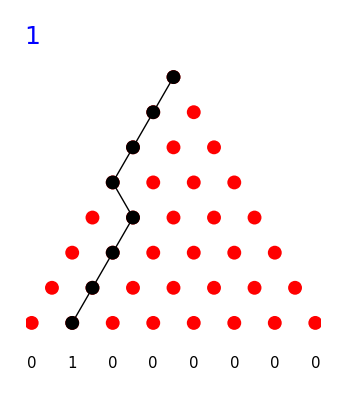
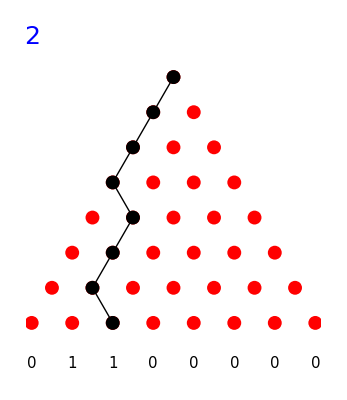
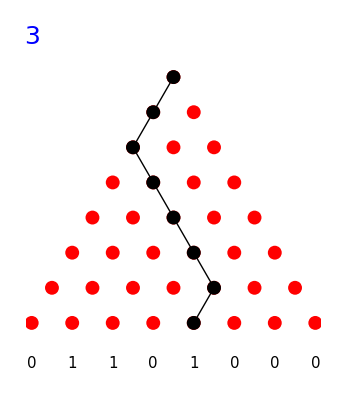
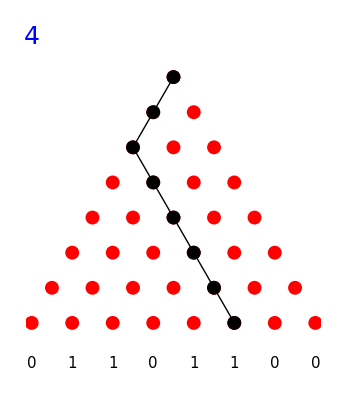
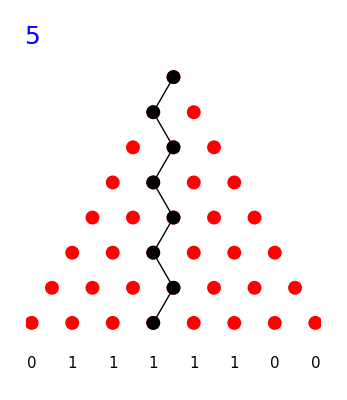
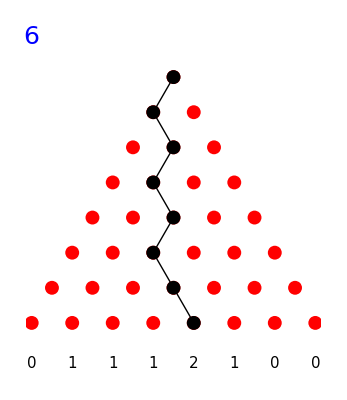
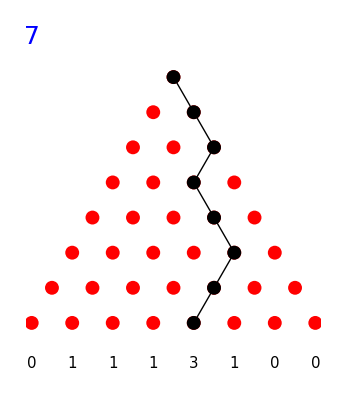
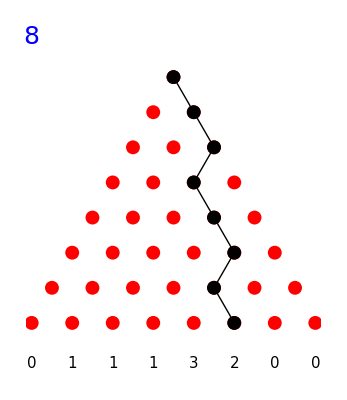

```mathematica
countView[8,10]
```

```mathematica
ListAnimate[countView[10,50],1]
```

Функция wayPoint[n,k] отображает список k*n кадров (каждое положение шарика при прохождении k маршрутов на доске размера n). На входе: размер доски, число шариков.

```mathematica
wayPoint[n_,k_]:=Block[{pointRoutes,pointFinals,pointCoords},pointRoutes=Flatten[Table[RandomChoice@giveAllRoutes[n],k],1]; pointFinals=Last/@pointRoutes;pointCoords=Flatten[ReplacePart[pointRoutes,{a_,b_}:>galtonBoard[n]⟦b,pointRoutes⟦a,b⟧⟧],1];
Table[Show[Graphics[{Text[Style[⌊i/n⌋,Blue,23],{First[Last[galtonBoard[n]]//First],1}],MapThread[Text[Style[#1,Black,17],#2]&,{Count[Take[pointFinals,⌊i/n⌋],#]&/@Range[1,n],{0,-1}+#&/@Last[galtonBoard[n]]}],AbsolutePointSize[12],Red,Point/@galtonBoard[n],Black,Point[pointCoords⟦i⟧]},ImageSize->Automatic]],{i,1,k*n}] ]
```

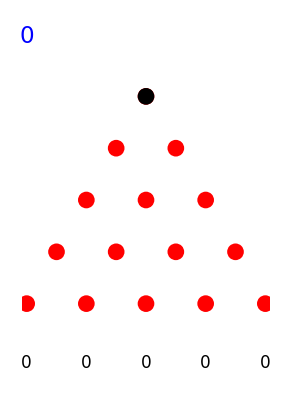
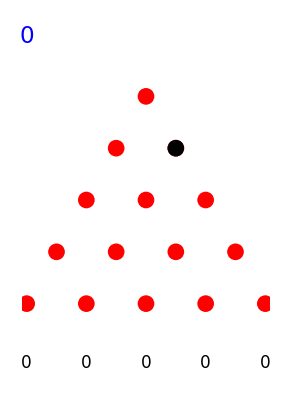
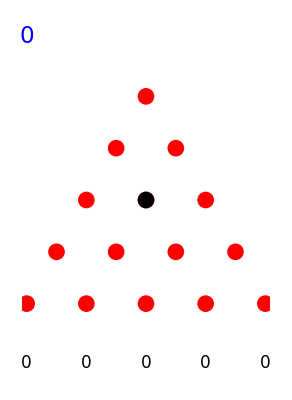
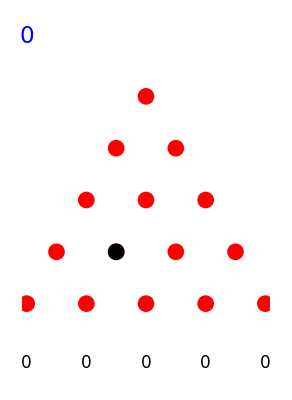
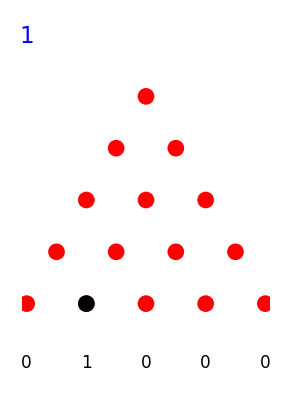
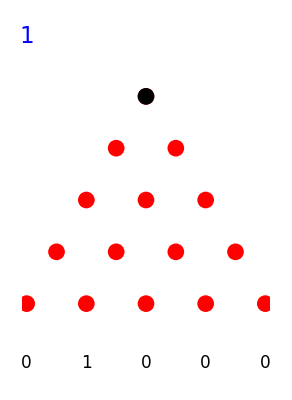
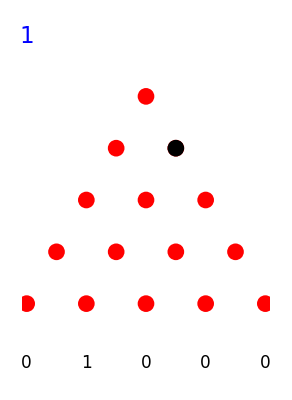
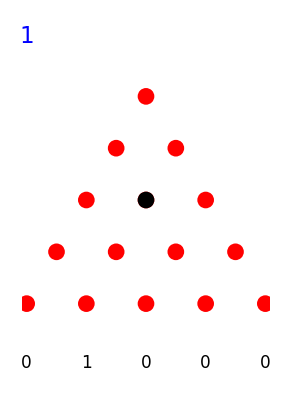

```mathematica
wayPoint[5,6]
```

wayPointAnimate[n,k] анимирует список кадров, вычисляемый функцией wayPoint[n,k].

```mathematica
wayPointAnimate[n_,k_]:=ListAnimate[wayPoint[n,k],3]
```

```mathematica
wayPointAnimate[6,10]
```